```mathematica
(* Dawid Bitner *)
(* zad1 *)
(* wycinek z mod4 *)
r[f_,x_]:=Module[{p={},sum=0,i,y,rand,win},Do[y=f[x[[i,1]],x[[i,2]]];
If[y≥0,sum=sum+y];,{i,1,Length[x]}];
(*losowanie osobnika*)rand=RandomInteger[{1,100}];
(*wybor ygranego ruletki z uwzglednianiem prawdopodobienstwa*)Do[y=f[x[[i,1]],x[[i,2]]];
If[y≥0,(*przyporządkowanie prawdopodobieństw*)AppendTo[p,Round[(y/sum)*100]];
(*warunki w celu wyłonienia zwyciężcy ruletki,każdy dopuszczony osobnikma przypożądkowane prawdopodobieństwo.Jeśli wylosowana liczba znajdzie się w ramach zakresu danego osobnika to zostaje zwycięzcą*)
If[rand>Total[p]-Last[p],If[rand≤Total[p],win=List[{x[[i,1]],x[[i,2]]}];];];];,{i,1,Length[x]}];
win 
(*Print[win]*)
];
(* SELEKCJA TURNIEJOWA *)
t[x_,n_]:=Module[{winner,i,r={},wi},Do[AppendTo[r,RandomInteger[{1,Length[x]}]];,{i,1,Length[x]}];
(*Wybór najczęściej losowanego indexu*)wi=Last[Keys[SortBy[Counts[r],Key]]];
(*Przypisanie do zwycięzcy wartości najczęściej losowanego osobnika*)winner=List[{x[[wi,1]],x[[wi,2]]}];
winner 
(*Print[winner]*)
];
(* KRZYŻOWANIE UŚREDNIAJĄCE *)
c[x_]:=Module[{c={},i},(*krzyżowanie wszystkich wektorów*)Do[AppendTo[c,x[[i,1]]+RandomReal[{0,1}]*(x[[i,2]]-x[[i,1]])];,{i,1,Length[x]}];
c
Print[c]
];
(* MUTACJA ZABURZAJĄCA *)
m[x_]:=Module[{y={},i,u={}},
(*poniżej następuje mutacja osobników*)
Do[
(*losowanie wektora*)
u=List[{RandomReal[{0,1}],RandomReal[{0,1}]}];
(*dodawanie wektora o rozkładzie Gaussa*)(*wektor zawierający liczby losowe zostaje transformowany Boxem-Mullerem do wektora liczb losowych o rozkładzie Gaussowskim*)AppendTo[y,{x[[i,1]]+Sqrt[-2*Log[u[[1,1]]]]*Cos[2*Pi*u[[1,2]]],x[[i,1]]+Sqrt[-2*Log[u[[1,1]]]]*Sin[2*Pi*u[[1,2]]]}];,{i,1,Length[x]}];
y 
(*Print[y]*)
];

(* ALGORYTM EWOLUCYJNY *)
e[fun_,N_,pc_,pm_,tMax_,z_]:=Module[{x={},i,yb,xb,j,y,changed,n=N, bests={}},(*populacja startowa*)x=Table[{RandomReal[{z[[1]],z[[2]]}],RandomReal[{z[[1]],z[[2]]}]},{i,1,N}];
(*wartości startowe są w tej chwili najlepsze*)xb=x[[1]];
yb=fun[x[[1,1]],x[[1,2]]];
Do[(*ocena populacji*)Do[y=fun[x[[j,1]],x[[j,2]]];
If[y<yb,yb=y;
xb={x[[j,1]],x[[j,2]]};];,{j,1,n}];
(*Selekcja i operacja genetyczna*)
(* mutacja, turniej *)
changed=m[t[x,N]];
(*ocena populacji*)If[fun[changed[[1,1]],changed[[1,2]]]<yb,yb=fun[changed[[1,1]],changed[[1,2]]];
xb={changed[[1,1]],changed[[1,2]]};];
(*sukcjesja*)
AppendTo[x,{changed[[1,1]],changed[[1,2]]}];
n=n+1;
AppendTo[bests,yb];
,{i,1,tMax}];
Print["Najlepsze x: ",xb," y: ",yb];
Print[ListPlot[bests,PlotLabel->"Przeieg zmienności najlepszych rozwiązań"]];
];
```

```mathematica
(*Funkcja wyszukująca najlepsze lokalne rozwiązanie wśród populacji (funkcja hybrydyzująca algorytm ewolucyjny)*)
h[x_, f_]:=Module[{winer, i, winValue, y},
(*Przypisywanie pierwszej wartości jako najlepszej*)
winer = x[[1]];
winValue=fun[x[[1,1]],x[[1,2]]];

(*Szukanie najlepszego lokalnego rozwiązania*)
Do[
y=fun[x[[i,1]],x[[i,2]]];
If[y<winValue,
winer=List[{x[[i, 1]], x[[i,2]]}];
winValue=y;];
,{i,1,Length[x]}];
winer

];
```

```mathematica
(*funkcja hybrydyzująca algorytm ewolucyjny*)
h[x_,f_]:=Module[{win,i,v,y},
(*pierwsza wartość najlepsza*)
win=x[[1]];
v=f[x[[1,1]],x[[1,2]]];
(*szukanie najlepszego lokalnego rozwiązania*)
Do[y=f[x[[i,1]],x[[i,2]]];
If[y<v,win=List[{x[[i,1]],x[[i,2]]}];
v=y;];,{i,1,Length[x]}];
win];
```

```mathematica
(*algorytm memetyczny*)M[f_,N_,pc_,pm_,tm_,r_]:=Module[{x={},i,yb,xb,j,y,ch,n=N,bests={}},(*populacja startowa*)x=Table[{RandomReal[{r[[1]],r[[2]]}],RandomReal[{r[[1]],r[[2]]}]},{i,1,n}];
(*wartości startowe póki co jako te najlepsze*)xb=x[[1]];
yb=f[x[[1,1]],x[[1,2]]];
Do[(*wybór najlepszych osobników*)Do[y=f[x[[j,1]],x[[j,2]]];
If[y<yb,yb=y;
xb={x[[j,1]],x[[j,2]]};];,{j,1,n}];
(*selekcja,operacja genetyczna i hybrydyzacja*)
ch=m[h[x,f]];
(*ocena populacji*)If[f[ch[[1,1]],ch[[1,2]]]<yb,yb=f[ch[[1,1]],ch[[1,2]]];
xb={ch[[1,1]],ch[[1,2]]};];
(*sukcesja*)AppendTo[x,{ch[[1,1]],ch[[1,2]]}];
n=n+1;
AppendTo[bests,yb];,{i,1,tm}];
Print["najlepsze x: ",xb,", f(x) : ",yb];
Print[ListPlot[bests,PlotLabel->"przebieg zmienności najlepszych rozwiązań"]];];
```

```mathematica
(* zad2 *)
(*Funkcje testowe*)
sphere[x_, y_]=x^2 + y^2;
ackley[x_,y_]= -20Exp[-0.2*Sqrt[0.5*(x^2+y^2)]]-Exp[0.5*(Cos[2*Pi*x]+Cos[2*Pi*y])]+E+20;
```

Najlepsze x: {-0.909102,0.98319} y: 1.79313

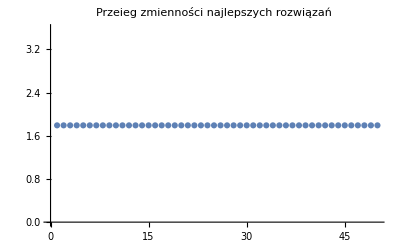

najlepsze x: {0.331719,0.105373}, f(x) : 0.121141

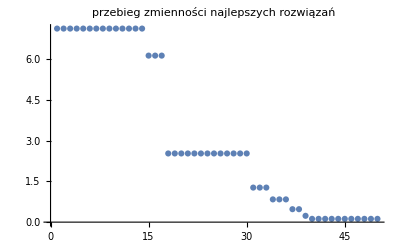

```mathematica
e[sphere, 10, 1, 1, 50, {-8,8}];
M[sphere, 10, 1, 1, 50, {-8,8}];
```

Najlepsze x: {0.0559783,0.876529} y: 2.76953

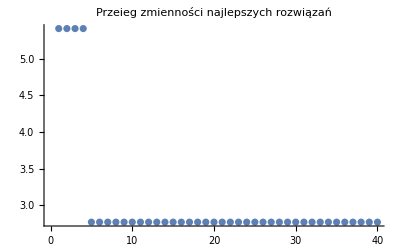

najlepsze x: {0.0529503,0.0373829}, f(x) : 0.29207

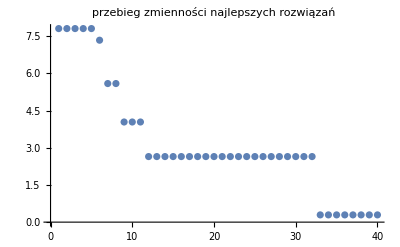

```mathematica
e[ackley, 20, 1, 1, 40, {-5,5}];
M[ackley, 20, 1, 1, 40, {-5,5}];
```

```mathematica
(*wniosek: metody po optymalizacji znajdują lepsze wyniki*)
```